声音

在 Wolfram 语言中，声音的工作原理与图形很像，只是没有像圆圈那样的东西，而是有音符。按下播放按钮  就可以实际播放声音。如果你不指定其它内容，Wolfram 语言会让音符听起来像在钢琴上弹奏的一样。

生成一个中央 C 音符：

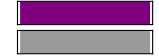

```mathematica
Sound[SoundNote["C"]]
```

你可以通过给出列表来指定一系列音符。

依次演奏三个音符：

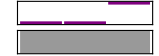

```mathematica
Sound[{SoundNote["C"],SoundNote["C"],SoundNote["G"]}]
```

你也可以用一个数字来指定它们的音高，而不是给出音符的名称。中央 C 是0，中央 C 以上每增加一个半音，就加 1。中央 G 比中央 C 高 7 个半音，所以用数字 7 来表示(一个八度是 12 个半音)。

用数字来指定音符：

```mathematica
Sound[{SoundNote[0],SoundNote[0],SoundNote[7]}]
```

-Graphics-

使用 Table 来生成连续 5 个音符：

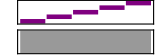

```mathematica
Sound[Table[SoundNote[n],{n,5}]]
```

如果你不指定其它参数，每个音符将持续 1 秒。使用 SoundNote[pitch,length]来获得不同的长度。

播放每个音符 0.1 秒：

```mathematica
Sound[Table[SoundNote[n,0.1],{n,5}]]
```

-Graphics-

除了钢琴之外，SoundNote 还可以处理很多其它的乐器。每种乐器的名称是一个字符串。

在模拟的小提琴上演奏音符：

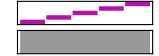

```mathematica
Sound[Table[SoundNote[n,0.1,"Violin"],{n,5}]]
```

要创建在每次生成时都不一样的“随机音乐”，也很容易。

连续播放 20 个随机音高的音符：

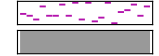

```mathematica
Sound[Table[SoundNote[RandomInteger[12],0.1,"Violin"],20]]
```

词汇

Sound[{...}] |   | 使用音符来创建声音
SoundNote["C"] |   | 命名的音符
SoundNote[5] |   | 使用数字来指定音高的音符
SoundNote[5,0.1] |   | 播放音符指定的时长
SoundNote[5,0.1,"Guitar"] |   | 使用某一乐器来播放音符

"共有 10 道习题"
"以及 4 道附加题" | "开始练习 »"

生成音高为 0、4 和 7 的音符序列。»

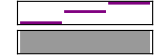
| 期望输出： |  
  | -Graphics- |

用大提琴(Cello)演奏 2 秒钟的中央  A  音符。»

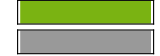
| 期望输出： |  
  | -Graphics- |

创建由音高从 0 到 48 的音符组成的 “riff”，步长为 1，每个音符持续 0.05 秒。»

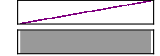
| 期望输出： |  
  | -Graphics- |

创建一个音符序列，音高从 12 下降到 0，步长为 1。»

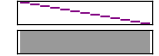
| 期望输出： |  
  | -Graphics- |

创建由 5 个音符组成的序列，从中央 C 开始，然后连续每次升一个八度(一个八度是 12 个半音)。»

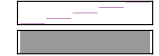
| 期望输出： |  
  | -Graphics- |

连续创建使用小号(Trumpet)演奏的 10 个音符，音高为 0 到 12 之间的随机数，持续时间为 0.2 秒。»

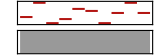
| 期望输出示例： |  
  | -Graphics- |

连续创建 10 个音符，音高为 12 以内的随机数，随机持续 10 分之 n 秒(n 不超过 10)。»

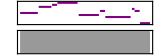
| 期望输出示例： |  
  | -Graphics- |

创建 0.1 秒的音符，其音高为 2^31 的各位数字。»

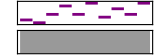
| 期望输出： |  
  | -Graphics- |

使用 CABBAGE 中的字母来创建声音，每个字母播放 0.3 秒，听起来像一把吉他。»

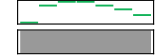
| 期望输出： |  
  | -Graphics- |

创建 0.1 秒的音符，其音高由 “wolfram” 中的字母的编号给出。»

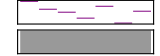
| 期望输出： |  
  | -Graphics- |

创建使用大提琴、钢琴(Piano)和吉他(Guitar)演奏的长度 1 秒的中央 D 的三个音符的序列。»

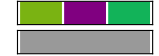
| 期望输出： |  
  | -Graphics- |

创建一个从音高 0 到音高 12 的音符序列，以 3 为步长上升。»

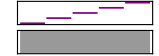
| 期望输出： |  
  | -Graphics- |

创建一个由 5 个音符组成的序列，从中央 C 开始，然后依次上升一个五度(7个半音)。»

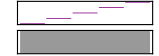
| 期望输出： |  
  | -Graphics- |

生成长度 0.02 秒的音符，音高由 1 到 200 之间的整数的名称的长度给出。»

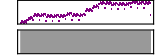
| 期望输出： |  
  | -Graphics- |

问&答

我如何知道哪些乐器是可用的？

看看 SoundNote 参考页中的“更多信息和选项”下的列表，或者直接开始输入，查看软件提供给你的自动完成列表。你也可以使用乐器编号，从1到128。所有的标准 MIDI 乐器都有，包括打击乐器。

如何演奏中央 C 以下的音符？

使用负数，比如 SoundNote[-10]。

升记号(sharp)和降记号(flat)音符叫什么？

E# (升 E), Ab (降 A)等等。它们也有编号(比如 E# 就是 5)。# 和 b 可以使用普通字符进行输入(虽然也可以使用特殊的 ♯ 和 ♭ 字符)。

如何创建一个和弦？

把音符名称放在一个列表中，比如 SoundNote[{"C","G"}]。

如何创建一个休止符？

对于0.2秒的休止符，使用 SoundNote[None,0.2]。

我怎样才能让一个声音立即播放，而不必按播放按钮？

使用 EmitSound，比如 EmitSound[Sound[SoundNote["C"]]]等等。

为什么在 “C “这样的音符名称中需要引号？

因为这个名字是一个 Wolfram 语言的字符串。如果你只输入 C，它将被解释为一个名为 C 的函数，这不是你想要的。

我可以录制音频并对其进行操作吗？

是的，使用 AudioCapture，然后使用像 AudioPlot、, Spectrogram、AudioPitchShift 等函数。

技术笔记

SoundNote 对应于 MIDI 声音。Wolfram 语言也支持“采样的声音”，比如使用 ListPlay 等函数，以及一个表示音频信号所有方面的 Audio 结构。

要获取语言输出，使用 Speak。要发出哔声，请使用 Beep。

探索更多

Wolfram 语言中的声音生成指南 »